## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "linux";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

```mathematica
For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames⟦i⟧]];
```

1: 00-Luft.DPT

2: 01-N10.DPT

3: 02-N50.DPT

4: 03-N100.DPT

5: 04-GaAs-undotiert.DPT

6: 05-GaAs-dotiert.DPT

7: 06-Si-undotiert.DPT

8: 07-R-GaAs-undotiert.DPT

9: 08-R-GaAs-dotiert.DPT

10: 09-R-Si-undotiert.DPT

11: 10-R-Si-dotiert.DPT

12: 11-T-GaAs-undotiert.DPT

13: 12-T-GaAs-dotiert.DPT

14: 13-T-Si-undotiert.DPT

15: 14-T-Si-dotiert.DPT

16: 15-R-GaAs-undotiert.DPT

17: 16-R-GaAs-dotiert.DPT

18: 17-R-Si-undotiert.DPT

19: 18-R-Si-dotiert.DPT

20: 19-T-GaAs-undotiert.DPT

21: 20-T-GaAs-dotiert.DPT

22: 21-T-Si-undotiert.DPT

23: 22-T-Si-dotiert.DPT

24: 99-A3-GaAs-dot-abgebrochen.DPT

25: 99-A3-GaAs-undot.DPT

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
dat0=data[0];
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->800];
```

```mathematica
Manipulate[ListPlot[data[n]],{n,0,22,1}]
```

```mathematica
Manipulate[ListPlot[data[n]⟦j;;j+k⟧,PlotRange->All],{{n,5},0,22,1},{{j,40000},60000,20,1},{{k,1000},100,10000,1}]
```

```mathematica
dfd=Fourier[data[5]⟦20000;;41000⟧];
```

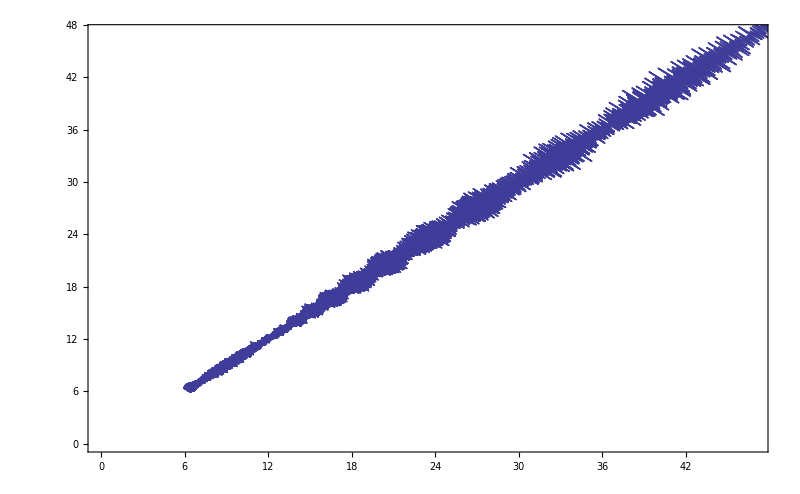

```mathematica
ListPlot[Abs[dfd]]
```

Reflexion GK 300-8000

```mathematica
rgk=Table[ListPlot[data[n],PlotStyle->Blue],{n,7,10,1}];
```

Reflexion TQ 1000-15000

```mathematica
rtq=Table[ListPlot[data[n],PlotStyle->Red],{n,15,18,1}];
```

Transmission GK 300-8000

```mathematica
tgk=Table[ListPlot[data[n],PlotStyle->Darker[Blue]],{n,11,14,1}];
```

Reflexion TQ 1000-15000

```mathematica
ttq=Table[ListPlot[data[n],PlotStyle->Darker[Red]],{n,19,22,1}];
```

```mathematica
im=2;
```

```mathematica
Manipulate[Show[{tgk⟦im⟧,ttq⟦im⟧}],{im,1,4,1}]
```

```mathematica
stretch[n_]:=(First[data[n]]⟦1⟧-Last[data[n]]⟦1⟧)/Length[data[n]]
```

```mathematica
join[n_,till_]:=Join[Reverse[data[n]]⟦1;;till⟧,Reverse[data[n+8]]⟦till+1;;3811⟧]
```

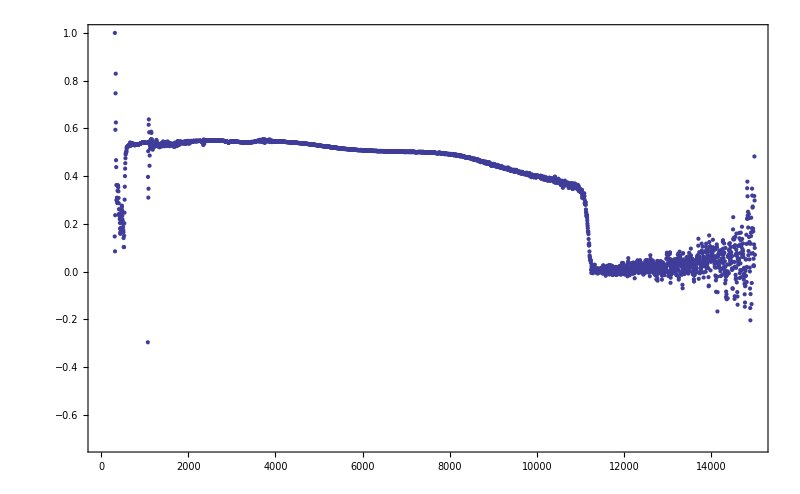

```mathematica
ListPlot[join[11,200]]
```

```mathematica
Dimensions[join[11,500]]
```

Part::span: begin ;; 500 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 501 ;; end is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: begin ;; 500 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part :: span will be suppressed during this calculation.

{4}

```mathematica
Reverse[data[19]]⟦51;;100⟧
```

{{493.77,1.25938},{497.628,0.32676},{501.485,0.74769},{505.343,0.74769},{509.2,0.74769},{513.058,0.77941},{516.915,2.75435},{520.773,2.75435},{524.631,2.75435},{528.488,0.69592},{532.346,0.28707},{536.203,-0.8752},{540.061,-0.8752},{543.919,-0.8752},{547.776,-0.8752},{551.634,0.0794},{555.491,0.22837},{559.349,1.13872},{563.206,1.13872},{567.064,1.13872},{570.922,0.06607},{574.779,-0.25079},{578.637,-0.35391},{582.494,-0.01877},{586.352,0.1065},{590.209,-0.22846},{594.067,-0.42285},{597.925,-0.14586},{601.782,-1.1013},{605.64,3.60286},{609.497,3.60286},{613.355,3.60286},{617.213,5.04736},{621.07,3.29128},{624.928,1.34094},{628.785,-0.91094},{632.643,-0.91094},{636.5,-0.91094},{640.358,0.34404},{644.216,0.58179},{648.073,0.37},{651.931,-1.18197},{655.788,1.13843},{659.646,1.13843},{663.503,1.13843},{667.361,1.13843},{671.219,0.94515},{675.076,1.27281},{678.934,1.07683},{682.791,0.783}}

```mathematica
Join[Reverse[data[11]]⟦1;;50⟧,Reverse[data[19]]⟦51;;100⟧]
```

{{300.891,-4.19217},{304.749,-4.19217},{308.606,-4.19217},{312.464,0.14743},{316.321,1.00031},{320.179,0.08508},{324.037,0.23663},{327.894,0.59442},{331.752,0.74726},{335.609,0.82947},{339.467,0.62504},{343.324,0.46696},{347.182,0.43798},{351.04,0.3627},{354.897,0.29925},{358.755,0.29975},{362.612,0.30896},{366.47,0.30945},{370.328,0.28783},{374.185,0.29102},{378.043,0.33888},{381.9,0.36173},{385.758,0.36155},{389.615,0.35759},{393.473,0.35348},{397.331,0.33665},{401.188,0.3088},{405.046,0.28687},{408.903,0.26176},{412.761,0.24256},{416.618,0.23646},{420.476,0.23916},{424.334,0.23248},{428.191,0.21983},{432.049,0.20388},{435.906,0.1801},{439.764,0.16064},{443.621,0.15863},{447.479,0.16493},{451.337,0.16921},{455.194,0.1838},{459.052,0.21238},{462.909,0.23416},{466.767,0.24939},{470.625,0.26596},{474.482,0.27671},{478.34,0.27357},{482.197,0.2566},{486.055,0.23453},{489.912,0.21949},{493.77,1.25938},{497.628,0.32676},{501.485,0.74769},{505.343,0.74769},{509.2,0.74769},{513.058,0.77941},{516.915,2.75435},{520.773,2.75435},{524.631,2.75435},{528.488,0.69592},{532.346,0.28707},{536.203,-0.8752},{540.061,-0.8752},{543.919,-0.8752},{547.776,-0.8752},{551.634,0.0794},{555.491,0.22837},{559.349,1.13872},{563.206,1.13872},{567.064,1.13872},{570.922,0.06607},{574.779,-0.25079},{578.637,-0.35391},{582.494,-0.01877},{586.352,0.1065},{590.209,-0.22846},{594.067,-0.42285},{597.925,-0.14586},{601.782,-1.1013},{605.64,3.60286},{609.497,3.60286},{613.355,3.60286},{617.213,5.04736},{621.07,3.29128},{624.928,1.34094},{628.785,-0.91094},{632.643,-0.91094},{636.5,-0.91094},{640.358,0.34404},{644.216,0.58179},{648.073,0.37},{651.931,-1.18197},{655.788,1.13843},{659.646,1.13843},{663.503,1.13843},{667.361,1.13843},{671.219,0.94515},{675.076,1.27281},{678.934,1.07683},{682.791,0.783}}

```mathematica
Dimensions[%]
```

{100,2}